```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Read in mat file

```mathematica
Import["Robot_Face_Ref.txt","Elements"]
```

{Data,Lines,Plaintext,String,Summary,Words}

The original meshes

```mathematica
Face=Import["Robot_Face_Ref.txt","Data"]+1;
```

```mathematica
VerticeRef=Import["Robot_Node_Ref.txt","Data"];
```

```mathematica
Dimensions[Face]
```

{10881,3}

```mathematica
Dimensions[VerticeRef]
```

{5562,3}

The parameterization results

```mathematica
UV=Import["Robot_UV.txt","Data"];
```

The principal directions and curvatures of the reference surface

```mathematica
PD1Ref=Import["Robot_PD1_Ref.txt","Data"];
PD2Ref=Import["Robot_PD2_Ref.txt","Data"];
k1Ref=Flatten[Import["Robot_k1_Ref.txt","Data"]];
k2Ref=Flatten[Import["Robot_k2_Ref.txt","Data"]];
```

```mathematica
Dimensions[k1Ref]
```

{5562}

```mathematica
nNodes=Dimensions[VerticeRef][[1]]
nFaces=Dimensions[Face][[1]]
```

5562

10881

modify Face orientation

```mathematica
NewFace=Table[{Face[[n,1]],Face[[n,3]],Face[[n,2]]},{n,1,nFaces}];
```

```mathematica
Face=NewFace;
```

```mathematica
Table[{{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,1]],3]]},{VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,2]],3]]},{VerticeRef[[Face[[n,3]],1]],VerticeRef[[Face[[n,3]],2]],VerticeRef[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelRef=Graphics3D[Polygon[%]]
```

-Graphics3D-

调整UV平面

```mathematica
(*旋转角度（以弧度为单位）*)
angle=180 Pi/180;
(*创建旋转变换函数*)
rotationTransform=RotationTransform[angle];
(*对所有节点进行旋转操作*)
rotatedNodes=rotationTransform/@UV;
```

```mathematica
Table[{{-rotatedNodes[[Face[[n,1]],1]],rotatedNodes[[Face[[n,1]],2]],0},{-rotatedNodes[[Face[[n,2]],1]],rotatedNodes[[Face[[n,2]],2]],0},{-rotatedNodes[[Face[[n,3]],1]],rotatedNodes[[Face[[n,3]],2]],0}},{n,1,nFaces}];
Graphics3D[Polygon[%]]
```

-Graphics3D-

```mathematica
UV=Table[{-rotatedNodes[[n,1]],rotatedNodes[[n,2]]},{n,1,nNodes}]//N
```

```mathematica
Table[{{UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],0},{UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],0},{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],0}},{n,1,nFaces}];
UVPlane=Graphics3D[Polygon[%]]
```

-Graphics3D-

```mathematica
Show[ModelRef,UVPlane]
```

-Graphics3D-

检查一下由Libigl计算的UV平面圆有多大

```mathematica
Max[UV[[All,1]]]-Min[UV[[All,1]]]
```

1.99994

```mathematica
Max[UV[[All,2]]]-Min[UV[[All,2]]]
```

1.99996

是一个半径几乎为1的圆

接下来要在半径几乎为1的圆上生成规则的网格，标准化的网格

计算混合积

```mathematica
MixProd=Table[({UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],1.0}).({UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],1.0}×{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],1.0}),{n,1,nFaces}];
```

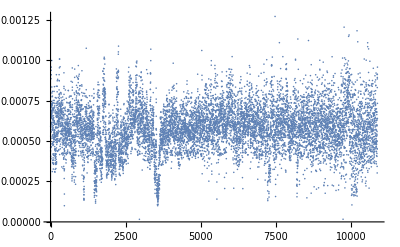

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{}

方法2：采用Mathematica提供的函数实现离散化

```mathematica
Rad=1;
FactorAssemb=0.001;
MeshSize=0.0003;
```

```mathematica
unitDisk=Disk[{0,0},Rad-FactorAssemb];
triangulationDisk=DiscretizeRegion[unitDisk,Method->Continuation,PerformanceGoal->"Quality",MeshQualityGoal->"Maximal",MaxCellMeasure->MeshSize];
Show[triangulationDisk,AspectRatio->Automatic];
```

```mathematica
(*获取节点和单元信息*)
UVRemesh=MeshCoordinates[triangulationDisk];
FaceRemesh=MeshCells[triangulationDisk,2];
(*2 表示获取三角形单元信息*)
```

```mathematica
nNodesRemesh=Dimensions[UVRemesh][[1]]
nFacesRemesh=Dimensions[FaceRemesh][[1]]
FaceRemesh=Table[FaceRemesh[[n,1]],{n,1,nFacesRemesh}];
```

8150

16030

```mathematica
Table[{{UVRemesh[[FaceRemesh[[n,1]],1]],UVRemesh[[FaceRemesh[[n,1]],2]],0},{UVRemesh[[FaceRemesh[[n,2]],1]],UVRemesh[[FaceRemesh[[n,2]],2]],0},{UVRemesh[[FaceRemesh[[n,3]],1]],UVRemesh[[FaceRemesh[[n,3]],2]],0}},{n,1,nFacesRemesh}];
Graphics3D[Polygon[%]]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,3]],1]],1/3(VerticeRef[[Face[[n,1]],1]]+VerticeRef[[Face[[n,2]],1]]+VerticeRef[[Face[[n,3]],1]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,0.468942,0.347303,0.162865},{1.,0.485693,0.368244,0.178854},{1.,0.46037,0.373297,0.171855},{1.,0.471668,0.362948,0.171191}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K21, K22, K23}

```mathematica
MatK2Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,3]],2]],1/3(VerticeRef[[Face[[n,1]],2]]+VerticeRef[[Face[[n,2]],2]]+VerticeRef[[Face[[n,3]],2]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,0.468942,0.347303,0.162865},{1.,0.485693,0.368244,0.178854},{1.,0.46037,0.373297,0.171855},{1.,0.471668,0.362948,0.171191}} 构成的 Inverse 的结果可能包含明显的数值错误.

{K31, K32, K33}

```mathematica
MatK3Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],3]],VerticeRef[[Face[[n,2]],3]],VerticeRef[[Face[[n,3]],3]],1/3(VerticeRef[[Face[[n,1]],3]]+VerticeRef[[Face[[n,2]],3]]+VerticeRef[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Inverse::luc: 病态矩阵 {{1.,0.468942,0.347303,0.162865},{1.,0.485693,0.368244,0.178854},{1.,0.46037,0.373297,0.171855},{1.,0.471668,0.362948,0.171191}} 构成的 Inverse 的结果可能包含明显的数值错误.

Check...

```mathematica
(*ListPlot[Table[MatK1Ref[[n,1]]+MatK1Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Ref[[n,1]]+MatK2Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Ref[[n,1]]+MatK3Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

```mathematica
Dimensions[MatK3Ref]
```

{10881,4}

上面得到了每个单元的K矩阵，可用于查询单元内部各点映射到曲面的坐标。接下来要给新的UV平面节点，匹配它所属的单元。

```mathematica
(*判断点是否位于任意一个三角形中*)
(*inTriangleQ[pt_,triVertices_]:=RegionMember[Triangle[triVertices],pt];*)
inTriangleQ[pt_,triVertices_]:=RegionMember[Polygon[triVertices],pt];
(*定义一个点的坐标*)
point={0.2,0.2};
(*找到包含给定点的三角形*)
triangleIndex=SelectFirst[Face,inTriangleQ[point,UV[[#]]]&]
Position[Face,triangleIndex][[1,1]]
```

{166,3373,3381}

3402

这条路行得通，接下来进入循环，如果新的UV平面圆与初始的平面圆一样大，会导致新的节点有可能落在初始平面圆的外面。于是缩小了一下新的UV平面圆。系数为FactorAssemb

一段计算不完，要分段以避免内存溢出

```mathematica
nNodesRemesh
```

8150

```mathematica
Pos=Table[0,{i,1,nNodesRemesh}];
```

```mathematica
n=1;
While[n<=nNodesRemesh,point={UVRemesh[[n,1]],UVRemesh[[n,2]]};triIndex=SelectFirst[Face,inTriangleQ[point,UV[[#]]]&];Pos[[n]]=Position[Face,triIndex][[1,1]];n++]
```

```mathematica
Pos
```

{5495,5950,5157,5952,9918,303,8585,7732,7732,318,2953,9781,7880,7880,5959,307,9713,9916,8447,386,3156,9746,9708,6134,6132,6131,6136,6137,5210,384,9784,5536,5537,9755,9372,6098,8920,5047,59,9724,3085,3085,361,3048,3046,3046,3049,8947,8947,3015,3013,9739,9739,3018,9914,2989,9738,2988,9259,9673,9801,5178,5177,7881,2955,9861,9861,5179,9737,9737,7882,9748,955,9788,329,329,7890,9767,3019,9741,9753,10516,9723,49,5524,3051,7405,3050,3054,3055,9733,9729,3090,9132,6075,1000,5530,10502,10341,6099,7900,3124,375,6139,5212,9757,9773,5213,8805,9881,3150,9769,3155,7206,1024,1024,943,5502,5166,2926,2954,9843,9782,319,7846,931,9926,5493,930,5955,9780,5941,5500,5500,5499,6354,6354,5069,5609,10680,85,9799,9770,9976,9987,10780,10744,10801,10714,10717,9939,10638,10567,10567,10301,10756,6878,6877,5113,10568,10160,5368,5367,9491,10600,1199,10723,7561,10872,6729,91,10671,4127,8862,8834,10651,7999,10605,4018,9417,6400,9225,8899,10563,10561,10558,10831,10843,10647,10575,6546,5676,5675,6632,9075,8113,5092,5092,5710,5708,10599,10599,10634,10733,5347,6630,5669,5665,5323,5323,6544,6473,4031,6472,7545,6474,488,6476,8095,6390,10161,6388,5269,6384,6386,10362,6646,6647,10412,493,10642,5353,10592,10565,10718,10842,10688,10594,4115,4115,10845,5790,6897,6898,6899,9763,9825,10810,1217,5796,10602,5799,92,10678,9833,9834,10658,7825,5601,9407,5598,9894,3945,9886,10498,3948,5607,5605,5038,9827,10635,7386,5707,6005,9910,5496,9820,1188,954,5606,5942,5709,7380,5607,9817,10556,5707,1189,9862,7381,9574,9911,6359,8919,373,8366,9064,10578,6406,6012,64,9897,5951,7821,10732,10482,9371,10556,10555,5955,9780,10623,10586,10587,10629,5710,2957,6006,2956,8711,9868,9895,9886,9882,9851,3948,9747,5266,6355,5499,6353,10098,6923,9936,10604,5365,7205,6123,981,3081,372,9795,7192,8446,7621,8817,8017,5375,10588,8310,8377,4085,10633,8492,4054,10621,10771,6392,8563,9575,9737,5516,7383,9783,1008,6092,9054,6118,383,9913,6040,10333,3036,5494,9929,9921,5950,5952,1215,10720,10870,5403,5085,10825,5600,1221,9893,929,8493,9701,9766,9823,9790,3952,1150,3957,6356,6365,5610,3955,1150,7524,10794,10799,10739,10637,7816,10773,10235,5781,6104,3127,5199,6140,8924,9742,9905,10378,7401,7669,358,7407,9735,9455,9734,9840,7934,5504,6399,8001,10606,8887,10643,5749,8129,6631,10093,10088,5673,10043,10676,5668,5322,10760,8659,5305,5271,10816,10366,7720,497,5044,7387,9459,9792,7195,7884,9527,9292,3123,9775,8855,7894,9200,7370,7844,8602,5542,5054,7419,3018,9914,9726,10319,5526,3039,9812,299,9917,9920,9919,7853,5159,10833,10827,10839,8595,10631,6726,6858,10609,10584,4057,10834,5599,1146,10667,6900,9926,9924,5931,5348,6639,9673,969,9127,1147,9902,9600,10641,5267,5603,6364,9658,6341,10805,10714,10734,10803,6926,10662,10034,10305,10832,6879,4185,5738,9756,9731,3126,9025,8769,8910,6102,9102,3125,7901,10553,9758,1020,50,9743,10530,3052,9866,9668,10549,6076,7897,6077,7893,10501,9831,9455,9841,7662,5040,5967,9427,5039,9203,941,9734,9829,9932,9761,9839,9874,942,5553,9325,8003,6396,7788,8000,10573,10684,10557,10616,10707,4135,10769,8834,10698,8861,10607,5670,5084,1181,5666,5671,5323,10685,5304,7545,8487,10710,5306,5270,6387,10632,6385,10692,7719,10655,7195,328,9835,9937,9506,9412,5198,9774,8543,5534,1009,9933,5534,9774,9787,999,9802,8162,9423,7371,9772,7372,7617,9791,9751,5208,7912,9027,8394,9931,6138,9914,9901,3014,979,7402,9907,3016,9908,3017,9739,6028,8541,9129,9128,6056,6057,7403,9777,7359,9922,9771,8599,10810,10823,10618,1213,10836,10657,10569,10603,10821,4114,10847,10856,10837,10840,10848,10619,5676,5674,5349,10876,10696,10696,6548,6547,8308,10647,4057,10670,8677,5601,5598,7635,10668,9816,1220,1148,5809,9808,4188,9764,10660,1218,5149,9927,2874,2879,9076,6641,5711,7382,327,8713,8653,9845,10533,9898,10640,6369,9799,6366,6368,7994,854,6367,7994,6367,7179,6370,10007,257,5884,9284,5469,5470,6364,6363,3956,5863,6363,7993,9191,6361,10795,10754,9942,10809,5417,10620,10567,10774,10820,10665,10589,9404,5740,3120,8606,9883,5544,7674,49,340,9727,10532,3053,6058,9935,9800,10497,3019,3091,3089,990,9733,9768,1000,9830,7620,9899,9811,9879,5207,6141,9814,7425,5553,1025,8485,4125,91,10695,7553,6721,8566,10737,10786,10781,10698,10648,10607,5667,6540,5665,10043,5672,6539,4050,6521,6538,6524,6543,4049,8075,5320,4050,6533,6530,6521,6523,10576,6629,6522,10759,5346,10612,10591,6545,10748,10727,10650,10766,7546,4017,8399,10571,10679,10704,10564,9579,9806,9836,9788,9506,9940,6023,6024,6026,6023,7121,7399,7121,334,6022,6027,2982,2982,6025,7387,6011,6010,7196,6011,5518,9717,5517,8923,5528,360,6072,9730,7733,3154,8869,2921,7423,9759,7732,9828,7880,9781,6137,9789,6135,6172,9746,384,5210,3038,10300,9129,6073,6067,5192,7406,8433,9101,3047,7617,7363,8585,9778,8538,5034,5927,7360,7362,7358,7362,7360,9869,7845,5928,7842,7843,5924,2867,7366,7361,300,7852,7361,925,5492,10731,8124,10738,10848,10751,8504,10718,10565,10592,8565,4187,10845,10619,6637,10826,10560,8868,10736,8928,10276,8483,8677,10831,5262,1222,5803,8137,5798,1219,6908,5800,5804,5115,9923,9941,9779,5711,2990,9259,8712,9882,10804,7178,855,9123,5130,8596,5946,2883,7636,10653,10824,9943,9946,9942,10803,10756,10505,10817,10807,6890,5739,8867,7908,9336,7889,3010,7400,7201,3054,9844,7192,7873,9428,7749,5545,7748,5206,5207,8580,8578,6169,7909,8761,6168,8441,7421,8270,5206,495,7560,10724,10722,6529,6521,6526,6527,5318,6620,10743,6544,10574,10590,8092,10783,10650,7149,7997,8400,6386,10701,10389,10656,9866,5184,7120,967,2968,324,7119,7389,8642,7744,5215,9822,9805,9804,5551,3156,8390,7743,6045,9915,6073,8844,8262,5191,3072,6063,3073,3063,362,8642,3075,6079,6091,351,8716,9870,5925,2869,5926,2868,5924,5939,5153,10614,10768,9988,7548,10825,10452,5806,10779,9233,868,5948,9946,6925,1198,10595,8510,10654,8266,6126,7890,7400,9720,970,8165,3143,7678,8436,7670,4126,10695,6728,10725,5101,5778,5747,10722,6626,10610,6619,6475,10783,8356,10387,10741,9579,6029,8367,7667,2961,8189,9803,318,2953,9804,9052,350,7202,3062,3097,6064,6003,923,7849,932,6859,10630,10689,10857,10858,4130,10644,8701,5949,5361,10545,6891,9796,8267,6152,8269,10188,10879,4134,9086,9019,6600,10576,8005,10363,10762,9349,6014,9022,7744,1371,351,8705,7848,5404,6855,10716,7558,8564,9999,89,10776,6703,6892,6154,7559,1204,6628,8464,10357,5370,10624,7197,4646,8153,10730,8503,9998,5098,7654,6690,6886,6893,8440,6625,7555,10796,10814,10344,10691,2969,4674,924,5408,6886,6887,1202,5741,10672,9818,301,9578,4082,7193,8539,9910,1149,6360,1010,7697,10676,321,370,5954,1216,9106,7892,48,997,3078,7203,3120,7665,8880,7873,7631,944,7621,5275,7694,8591,8792,7787,8819,8889,8013,5620,9065,8890,8467,5277,9519,9447,9447,63,9454,9409,1019,7755,9849,6122,9907,9889,3008,8785,3037,6052,10850,10853,5795,10852,10828,9449,9437,5784,5787,5782,9169,8636,9219,6874,10240,10203,5085,9074,9033,5602,10449,7635,9891,9888,8115,6633,9765,8801,9857,5264,6125,3144,3128,7935,9813,9204,7936,7426,385,8484,8019,10721,3118,370,6097,6068,6056,10359,8435,9131,3074,10731,8409,10822,8090,8096,10690,5801,10458,6059,3020,339,3045,10491,9798,9810,9740,337,4697,8261,8260,7893,3056,3077,6078,6071,5533,3069,3080,9218,7372,5960,7371,7928,9751,9815,8603,9056,7735,9289,7736,9197,8587,7756,8393,8525,7128,8770,7424,5218,2866,8425,5156,5947,5944,10377,10327,10127,971,10303,3012,3004,6043,6041,7891,3011,3004,7401,3012,2923,7670,5697,10611,10706,4083,10686,964,7389,9279,323,6008,9832,8430,7728,7878,5490,9091,9346,7623,8783,8569,7872,8866,8602,7870,341,3099,9166,7849,5154,5939,5498,9220,10280,10652,4174,6861,6856,5748,6727,6837,9343,1204,10451,8637,6705,5395,8506,6705,8379,4109,6693,6692,4109,6927,6689,5736,7815,5416,8781,6688,6689,8120,8138,4195,8120,8918,9108,8932,9153,8919,8465,8125,9181,9170,9063,10812,7537,7537,7782,5273,10813,10813,8008,6404,8374,9012,8009,8620,9031,8011,8374,4183,4141,4143,6751,6880,6884,6880,6881,6883,4181,6888,6702,4111,5364,6697,6687,6702,4111,6696,5365,6692,7244,5744,8779,8778,90,8127,10712,5372,7554,8128,10682,7549,7551,5371,7552,8562,8516,6708,4116,4117,8125,9819,927,7716,9639,7194,46,9912,5934,5535,6129,3147,6128,3146,7420,7672,1015,5205,3139,7412,3148,7698,7122,368,7409,6088,7409,6090,3101,8264,369,7898,3113,6090,10827,8432,7892,3043,6055,349,6054,980,3044,8981,6049,6053,9176,52,51,1379,4691,986,984,2999,3001,985,1384,4695,7077,4696,4706,6033,6034,976,3003,3000,6069,9853,7896,998,5996,5997,5515,5043,7624,8881,9838,944,5552,7152,8505,7817,10880,7818,9299,10195,6718,9232,10309,10278,10196,9518,4020,5393,6808,6810,6802,4162,5394,9283,8931,6807,9308,5106,9309,10260,7553,7655,1200,5627,5627,4158,6809,10270,10269,5628,7793,6677,6803,6798,6796,6793,4122,8313,5277,6426,6674,4159,6806,6804,5392,4122,5073,6800,5095,8774,6416,1193,7640,9050,8028,5284,5282,8031,8029,5359,5720,1194,5725,6842,1195,8611,6797,1031,8745,4156,5386,9580,5769,6795,6794,5768,1209,5724,6665,6664,5767,8395,6663,5358,6847,6848,4155,4171,4169,6838,6846,6848,6843,6844,6836,4172,5759,6844,5761,5761,6749,6837,6840,9432,5401,6845,5760,5400,6832,6830,8942,8888,8622,8018,8012,6409,7695,7706,8018,8015,8089,8482,8467,7854,5160,9109,8921,8878,9444,9425,9053,7855,7106,7106,9020,8426,7856,5971,9410,9322,5174,9238,8570,5173,5169,5995,5994,9290,9238,8570,7736,9867,7871,7869,7746,5541,5202,5203,3009,6039,330,3006,3007,336,8785,347,53,8765,5783,8646,6851,6850,6868,6862,5112,6869,10854,10863,5783,5405,10226,5097,5727,7814,5733,10224,8498,10200,8776,5729,10255,6870,6871,4175,6706,6853,5403,6682,4107,5731,4177,10861,10772,6684,8311,9293,5360,4177,5774,5772,10868,10768,9199,8838,6678,5731,5730,4105,1212,10859,8930,1196,5751,9089,9213,5752,6683,8635,6683,6234,8787,6235,9443,5750,5399,5754,5102,5108,5755,6188,1210,1211,4163,6814,6815,5777,6818,8134,9186,5396,5395,8507,6734,4140,5773,9431,9152,6732,4139,6825,6733,8360,6826,6747,9269,6731,6743,5557,8831,5785,8410,8411,5793,10697,6909,10697,10582,6909,10866,8511,4108,5325,4058,6554,4088,9151,9033,10459,8738,8772,3943,3941,10449,7847,6634,9077,6633,8768,6343,5263,9855,10753,4189,988,3111,3082,8263,1005,3070,58,367,367,3110,3110,3104,61,1007,1004,359,4821,359,372,6085,1374,3122,5194,5197,4665,3119,3107,8717,7899,6085,3105,6096,6084,8856,6082,364,365,3103,3102,7422,382,3140,9846,6113,6118,6121,10042,7418,10508,9177,3151,5201,9261,10041,9134,613,9846,3142,382,5052,6119,10543,3141,6145,8655,3135,6087,6086,10507,9373,8605,3133,6087,378,3135,8265,10508,5201,5945,2653,7850,10378,7937,5964,5344,6624,9594,2970,7395,8255,7844,3061,345,2877,5152,933,5748,8406,8764,8748,5374,4129,6722,6689,6241,9944,7781,8082,8085,4182,10672,2879,302,9311,298,928,2880,41,7731,7731,7659,5352,4082,4089,6623,6621,10749,9714,4091,9701,6620,7384,960,2959,959,46,958,8908,8654,9823,7391,5604,5497,6348,5932,5935,2878,9281,3951,6346,2877,8267,7911,5196,363,3041,989,3045,5190,9222,6050,6054,4683,992,355,4796,1383,5454,5996,7118,5165,7858,7858,5106,9307,6805,8746,6676,5285,10106,6421,6420,8030,8049,5289,1171,6422,5283,6427,8051,8038,8051,7144,6436,8357,8480,10107,10139,7644,8117,7799,8046,7642,6424,8624,5639,10140,9439,4024,6443,6428,7464,8872,6675,8830,4024,8052,6434,8045,8740,4025,6669,8827,8050,8519,6287,9438,8550,9374,8118,7429,4102,7430,8829,4103,6667,5096,5719,9348,6671,10418,6182,5359,10084,6180,3159,7939,8588,7208,4100,6261,1030,10393,8612,8395,5229,8528,3161,6212,7942,8528,3175,6185,9954,391,6418,10234,4148,6766,6764,8380,8380,5757,6763,6757,5780,5110,6833,6834,6835,8818,7696,7676,6158,6161,9760,7422,5961,9104,6149,7929,6162,5984,5169,8708,3007,972,3025,6051,7668,4176,5777,8509,8135,8638,6817,10868,10862,4178,6874,6679,6216,4106,8584,5411,8845,395,7129,6238,8517,9017,9406,6678,5381,5380,7433,7562,8496,7761,3176,6744,9476,6213,5226,10476,5555,8526,5230,6217,498,7941,10471,7940,6219,8272,9205,6824,6827,8508,7726,6736,8132,6745,1029,1029,6742,4138,6737,8500,10802,7847,2847,9878,9876,5929,9875,5491,7742,7729,9887,8586,5491,6634,5351,9077,8768,5046,2986,7886,7199,7109,5520,10004,6038,9357,2994,8368,5264,9415,5263,8087,8086,10747,5302,10753,8994,10767,6468,6468,8088,10139,6470,7646,9093,8068,5294,8897,6451,9226,6903,7563,6906,9561,6902,8316,5118,5116,4190,6901,6905,5410,4189,5409,6911,6910,6912,6918,4192,6904,6919,5413,7211,8316,5479,7564,897,8909,6332,7347,10496,10512,6333,5480,6331,9807,5261,10492,32,1037,5414,10713,10700,10673,2757,1036,10496,9785,10683,10490,256,5135,5882,6337,9994,9951,2753,7348,2738,2754,5880,2751,7181,898,5566,5566,3193,630,631,4662,4658,4663,5451,6084,381,7417,380,7904,9133,5449,7417,1017,7111,7415,7414,6115,7416,7123,3136,1022,8542,3138,7049,3137,5549,7903,5053,7125,4629,1023,8146,7628,4629,7922,8351,6150,5550,8164,6152,8144,5513,7046,7014,6156,7921,2933,6155,3152,8147,6152,8146,8387,4639,7752,5512,6156,8369,7587,7093,7924,7124,8439,9029,3153,8148,7050,622,6171,9059,9011,5511,7107,5978,7865,7622,7866,2934,5975,43,9021,5974,7049,4640,121,9116,4556,617,7588,4856,5975,9173,1358,1365,8329,5842,9596,4637,7092,661,8330,7916,8884,8608,7914,8607,5214,6120,3134,10358,3132,3100,7898,619,10361,3131,5200,4632,6109,5531,4631,3096,1002,4650,7590,5532,4654,1003,5450,6080,626,3092,122,4651,7059,4647,7051,127,4644,4646,4652,4646,126,4830,7065,4655,9047,5452,628,8337,7066,629,4656,5843,7061,619,8327,5450,4675,4672,3058,4831,1355,4673,4677,3059,3061,3060,4655,1360,8149,5189,3027,3033,6061,4668,4689,1375,130,7064,4806,1369,4667,4676,4678,1363,4633,621,4636,5455,123,122,1354,4816,7053,1356,8914,5448,7585,7052,4620,7586,9000,5447,7661,7661,9040,7332,2652,8416,2603,7327,8159,5861,2655,2859,2653,5146,2864,5920,294,2856,2860,5921,38,294,921,5921,2858,283,2830,282,2861,2828,2825,2823,2857,922,5919,8536,2872,2871,5930,2847,40,289,7185,2856,2848,5489,7356,5489,38,5915,2846,2922,4084,5344,6624,4084,7714,6579,5692,5692,6595,5692,5338,5699,1185,5702,5697,9553,2962,9553,9585,9718,9158,9570,9570,9391,4736,9718,651,964,4733,8187,4734,4715,8155,4741,962,1391,4741,1390,4739,5182,650,4749,4749,1394,4751,4876,4756,2965,645,5181,4720,6018,2974,9024,9024,5519,7108,5183,7394,4712,4711,7079,4714,1390,4717,7108,3036,7658,5937,925,5152,8154,2592,2849,8247,8703,5936,8247,23,5152,5472,2876,5373,5746,3199,10441,7443,7565,5415,6241,5886,7182,8870,10410,6924,10441,10433,6924,10434,8547,10433,10457,8649,2624,9981,10455,894,9975,2762,7349,2762,9690,7349,5057,6240,5567,1040,8789,5478,2761,5131,7566,6242,6248,2743,895,5885,7329,2612,2611,5864,400,3200,3215,30,10325,8417,9310,257,5132,402,6224,3182,402,393,3201,8448,8276,3214,3202,3216,408,6247,255,6246,7345,8721,2749,31,2742,2741,2746,2744,2609,9257,10059,9965,10307,2610,10156,10155,222,10155,10147,2627,10083,10308,10058,9683,9950,860,859,9672,10135,22,9964,9435,9644,9531,9689,9689,5867,9672,9947,9153,6464,9013,6464,8083,6463,9070,8078,8077,9070,5300,7242,8082,8927,7241,8629,8026,8080,8066,8078,9268,8076,10537,8478,8079,10131,5299,8076,7808,6534,10322,8466,8619,7785,9669,6450,10130,6537,8006,9652,5280,8477,10129,6536,9312,5312,6499,5319,9315,10337,8470,8477,5654,4051,6537,6535,6537,8025,6781,6410,7699,4019,6411,7784,10337,5279,9651,9216,8775,10367,8891,7789,6448,5072,8916,8926,9295,9231,8473,9296,7812,5652,6525,10057,5656,5081,4037,9515,8995,9032,6447,10000,10060,9719,5653,5636,9560,8626,7703,9638,10057,9418,9512,5648,6494,4035,5308,491,5311,9706,10728,10784,6622,8423,9229,10448,3071,3079,6065,6070,9555,354,3065,56,9388,7068,8802,634,4681,4683,4680,8950,8958,4679,4682,8949,342,993,4685,3066,352,3067,635,1380,4813,4812,9358,1378,9388,4679,3028,8982,4693,9302,8434,4666,1373,7083,9696,4822,4808,9003,8753,7085,4811,8865,7598,5457,10012,8842,7062,4661,4821,4819,4825,4823,4839,1412,4825,4916,9986,4931,9972,4819,7255,4808,4690,637,4691,1406,4812,4797,4814,4803,1407,4799,4798,4802,673,672,4912,8345,652,1432,10489,4903,671,8199,8756,7258,4973,2997,4702,4725,8431,7740,5912,8882,7741,7103,7877,904,8537,2842,2947,2947,8883,2949,5176,8945,5989,2946,5988,45,5484,2774,9347,8521,2776,2943,5171,5989,9328,4492,5167,9278,2951,2948,2950,9445,5978,7865,8252,2935,5167,9445,7861,2925,8034,8034,6455,5296,8480,8069,5296,6435,8048,8060,7465,7687,8451,8610,3158,388,3292,3235,6209,6208,6199,3173,6205,9008,5564,3167,10420,66,8548,9136,9955,6266,5281,7240,1172,6419,6417,4144,4147,5382,6748,6748,4146,4144,6752,6698,4112,8833,6695,5362,6700,6754,5383,5383,9776,9240,8444,7931,10006,7127,7932,5216,6148,7929,5970,2927,9058,7862,7862,7675,8656,8874,7750,5042,5969,946,7191,5501,7734,10046,10047,9028,8579,5969,2929,309,5969,5163,9458,7863,7105,42,5162,5162,6164,6146,8885,5506,5041,5507,5972,8389,1021,5972,2928,5547,8392,7751,4542,5546,7915,6143,613,7040,5508,945,7000,4543,5505,4545,7581,4541,7009,7036,2931,8251,5168,8799,7864,8641,5984,5983,5982,8877,5982,7377,8253,8254,2764,315,952,8793,314,949,2769,44,258,8793,5887,900,5888,5031,2765,903,2763,260,2767,5514,4483,901,2770,7350,901,5032,5888,5990,5991,7102,331,2992,9156,5522,9291,5185,974,9001,641,4701,1382,8331,640,636,7069,7592,10493,9002,4787,8514,9084,4899,4790,4778,10488,8681,4792,10493,4791,10513,8177,4688,9389,4686,8513,8176,5844,1377,654,4805,8177,8335,6036,3022,6871,6864,6239,396,6237,7440,9424,5360,10227,8354,5125,6825,4165,6820,6821,8660,6190,3162,4137,4138,1191,5376,5712,5713,6738,5223,6658,5148,7657,9884,7840,9887,7838,9904,9877,9878,7185,7742,9880,5930,4087,5351,5350,6636,5339,10869,10869,4078,5705,9666,5351,9313,9175,2987,2975,9707,6015,7397,326,7887,6020,325,9168,2985,3950,5265,6345,9415,5862,218,9415,853,2605,5468,9414,852,5862,7098,6349,6350,10878,6551,10797,4191,6913,8837,8837,6916,6236,8459,6335,6335,9207,32,1036,3196,1039,3192,5412,4664,4643,1016,5540,4641,1018,7057,125,624,8841,4628,8864,7046,7049,7679,7757,947,5164,2923,5963,311,5980,5966,7857,8427,8752,5458,9571,137,9394,4835,134,4835,4834,1366,4836,5538,7626,5048,3129,8904,6107,1013,8326,8190,8905,9189,4818,4817,1362,54,54,4670,3026,6048,3035,7071,7070,5525,3022,3024,4833,9221,4847,9079,9194,7035,615,8839,4624,9597,9534,8244,5860,2601,2641,226,2656,2657,10326,226,2602,2656,226,2642,2601,2863,297,5922,872,2829,2822,4075,6597,6490,5655,4076,6596,5658,1179,4072,4076,1179,6598,8111,4755,1397,4866,9005,4755,9274,9273,4731,1401,4745,4753,9655,1392,1400,4724,4768,8258,9640,1395,9117,4869,9157,8341,1402,292,8364,8245,2852,5916,8704,2854,919,2855,8796,8650,2855,8245,2832,5488,6724,5743,10345,8850,4131,4132,5100,5100,10809,6340,9982,8419,8418,7692,8418,7692,10708,10778,10785,10792,6691,8902,7566,8902,5232,3184,6228,3186,394,3183,3226,3212,412,9477,1035,6229,9949,9429,5562,8984,9489,6230,3225,3189,6232,406,8209,3213,2743,8702,867,9682,9684,9474,7148,7649,6459,6462,6461,6542,8075,5645,10746,1174,5644,6541,7637,8401,9062,7637,6414,7638,6413,6652,6791,1170,5624,5621,6650,4095,6785,4153,10037,4152,7725,6651,7724,6651,5390,6769,6786,5715,6654,5094,4097,4093,4098,6649,6661,6661,7639,8041,9210,8658,6627,6525,9970,7243,7243,4090,6622,2875,8423,9625,9616,6065,4838,4838,4927,4923,4928,4930,4926,4942,2914,9615,5022,138,5012,7257,1442,1437,5018,9959,5005,3914,1450,5004,4918,5007,4917,5015,5013,7602,4910,656,4815,4911,1435,5006,5008,4815,3904,4993,3903,8346,4826,4795,4983,4985,4995,1433,10520,4985,4997,9324,4894,4786,4890,4881,4889,4976,4882,4895,4769,4763,4783,4781,8157,8156,4891,4975,7613,9698,4974,1427,4964,8759,8759,3870,4965,1423,9699,8344,1424,4949,4952,4950,3831,4967,3845,3846,7610,4955,3834,4858,4952,4871,4868,4867,4870,642,4780,4704,131,4705,4702,7379,6002,8710,2952,5175,7874,6000,7875,9057,7876,5999,6001,904,2845,2841,2840,2846,907,4550,5986,9411,2945,2943,4496,4553,7583,7663,9427,7860,7860,6454,7647,5291,6440,6437,7708,6445,8057,7804,7541,8047,6444,8062,7805,5076,8307,6446,7541,4030,7146,8723,6485,487,7702,4029,7969,5637,6329,3278,8106,7458,4034,8594,3274,8858,8574,429,490,9087,8103,3276,6280,7457,6328,7690,8812,7967,3275,3281,5246,8657,8657,7972,7760,6288,5580,7954,7957,7955,7958,3236,5243,3172,9090,6204,5227,6200,7954,6766,8452,9954,709,6267,7953,6266,7964,8811,1725,9262,419,8935,6765,3167,6759,5384,7927,7630,7424,7039,614,5437,4522,4521,590,5437,1326,10351,4520,4540,6998,4524,7001,113,4541,4539,4544,4537,4486,1314,594,7008,7010,8520,4480,9552,2937,4480,4478,2938,312,2940,4477,5982,2768,8794,9009,277,7837,2818,2835,2817,916,8420,2836,8795,8421,8766,8598,278,8598,4484,575,8663,4481,577,4483,4486,1294,4456,4487,4457,4485,4488,577,6980,5482,567,5432,5172,5992,2838,285,5992,5991,331,973,972,972,5521,2995,9260,2996,335,5186,3005,6047,8332,1385,4698,4699,4718,9160,9162,4901,10552,10101,133,653,4909,1409,655,9896,6037,6037,3198,3191,3190,3194,397,5235,5561,8643,6214,7943,3176,8274,7437,392,3179,8449,6222,5569,1041,69,6252,5569,3220,1549,3218,3221,3180,10479,6740,9030,9206,6191,7819,4136,4136,6828,6829,1208,5766,5093,5718,5764,5762,5714,5717,5105,2873,6638,6603,6553,9485,6645,5701,5703,5091,9618,5706,1187,6601,8824,5704,10253,4077,6604,6615,6608,7715,8309,10256,8195,5316,10242,5089,1186,10124,6607,5695,5343,6582,10110,10109,6614,6569,4081,4079,5082,6612,10171,6606,6613,6610,6516,5315,4044,5315,6510,6500,6509,6513,4040,5083,6512,5659,6507,6503,5313,4038,492,4041,6505,5640,7809,5641,5298,6471,9522,6504,6506,6502,6503,6501,6508,6456,5303,5642,9093,5077,8070,7544,8994,6549,5663,5324,6453,8073,8900,6458,8561,8073,5314,5309,6481,5310,6482,5651,6483,8574,7709,10138,6486,1177,6519,8823,8929,8397,8791,6489,6575,5593,7776,7634,8901,7779,5330,6517,4080,7986,9087,6574,7653,5650,7987,8458,10193,6560,8405,6571,7634,8554,10194,9577,8173,4066,6577,6576,8491,5683,5332,6558,6560,7771,5590,6578,9321,8173,9048,7778,9171,5067,6323,3339,7989,7980,7140,7775,9103,6316,7689,6318,8455,7979,9018,7773,6315,5590,7770,4059,5258,3340,6317,1074,6320,9765,3949,5883,9286,10028,7328,9952,9256,9967,856,2606,2755,220,857,21,856,858,252,253,893,5477,29,892,893,7948,9495,893,2734,250,251,398,2735,2731,725,727,2733,9953,6239,68,8939,3195,8700,2613,2617,2613,2620,2616,235,2618,2632,5865,2631,9340,2632,219,8597,9042,8688,2686,1760,9041,2687,2635,6349,3953,6351,5151,6352,2644,7331,851,10069,2643,10069,2646,863,228,2648,6548,10715,6551,10788,6550,9182,6914,6234,3152,4558,7005,7868,8798,8427,121,8752,8903,5833,1328,9014,7047,7045,4535,7042,7044,5838,7254,7252,4851,4530,4854,4529,9246,1330,4527,9188,5123,7043,4856,1421,4924,4925,9647,9647,9401,1422,9649,4945,7608,9590,1160,8347,7529,4941,9038,9047,10052,4669,3021,9532,621,658,7089,1415,4828,4921,9227,1414,9973,7090,10014,8178,10014,10015,136,7616,663,4938,664,4935,4936,7091,1415,659,4842,4623,589,4522,4519,4516,4518,4625,6997,4578,5441,7021,601,9037,7022,4581,864,8244,850,2597,2831,5910,873,874,2826,5143,5909,35,5908,2805,2824,2801,2673,2830,2712,2800,5476,2802,2669,5900,2666,2668,9408,2819,2820,2804,280,8363,5914,8522,5145,8522,6591,6594,9460,4732,648,7198,968,4728,4723,4729,4725,4724,9117,4748,4862,4861,4748,4858,4946,7612,4947,3848,4959,3842,4962,3849,4960,3850,3865,3839,7512,4957,3838,3844,3837,3840,3843,3819,3866,4970,7516,3813,8557,4957,4969,4972,7520,4980,3880,4968,3863,8559,8558,8859,3822,3873,3864,1135,3872,3857,3879,4879,4874,4979,3877,4990,3889,9267,4981,9267,4896,4991,4988,1445,7513,8859,3797,3804,8735,3856,3783,8295,3873,10472,8989,9148,8296,3884,1425,1426,4880,1429,4757,4977,4906,1446,3807,7509,8299,3858,3885,10548,3888,9448,10394,10391,10430,8913,4971,1443,670,4877,4762,5002,10536,10524,4897,1431,7601,10488,7504,3810,3825,3822,3821,3794,3777,4772,4722,1389,5003,4907,10551,3860,3790,3803,7507,3779,3781,1429,1403,4774,4720,132,3789,3853,3788,9722,3792,3791,9525,3802,3809,4888,3790,9665,9380,9630,3786,9662,3680,3725,3785,3774,9484,3706,3680,3797,3705,3717,3707,3700,3727,3718,3735,3737,9958,3745,3748,3828,9368,3743,3741,3723,3817,3815,3828,7511,3827,9586,8733,8288,3731,9557,9969,9488,4752,2868,2870,7836,7656,7656,2834,7354,2833,7102,2832,5744,5745,4193,6225,6686,8122,494,7438,3203,3185,7944,6226,7439,5565,1034,5565,6253,7762,3169,6206,7444,7445,7955,158,2750,729,730,8722,3210,682,1045,3229,1043,3227,1578,1627,1561,1556,1757,1045,9671,7163,1752,1768,1753,1775,1751,9657,1755,1767,724,9469,1756,9535,683,724,683,1769,1574,1573,1746,9118,1743,1775,9684,7242,4118,6711,5618,8023,6792,4152,5388,6782,6778,6783,6710,6776,5369,6709,8126,4119,6777,5387,4151,6654,6655,6429,8039,8625,6431,7790,7791,10095,10277,5554,6656,8494,8116,6189,6662,4099,5225,6187,6187,10315,6178,6177,8627,8065,7801,7703,8471,5622,9202,8626,5634,486,8358,7800,9595,7801,5635,485,8633,8056,8633,8892,4026,8102,8476,9217,484,6432,6432,9316,9678,9067,7539,4027,8741,6438,7540,7145,8054,8053,8375,8894,489,10163,5308,4940,5025,7530,3931,5023,3928,939,1162,3927,2920,1163,7531,1161,7996,3995,3996,2918,7532,7369,3998,478,938,9277,4770,4766,4781,4895,1444,10526,3881,10519,3890,1139,9263,1140,3886,3892,3871,1139,9604,3894,3907,1136,3868,3887,3859,3874,3875,9559,4784,4710,4708,4707,4709,287,2843,4554,2778,5170,5891,263,5987,262,5892,1308,2779,2777,8751,4489,2779,34,34,33,905,5893,7580,2781,5139,4473,273,5486,574,264,1310,579,4495,5829,580,2944,5248,10450,3294,10251,3295,10439,7971,1026,417,1063,5581,8893,8531,7958,694,7973,3247,7130,114,4525,585,1319,1323,4560,5830,5832,1334,4497,4583,6992,4600,4599,4505,7027,4502,606,10349,6990,4504,4503,1312,1312,578,4561,4561,10423,4498,1333,10432,951,2810,2814,37,36,2769,269,5488,284,8323,6978,5890,2772,5138,268,2771,2836,286,286,8184,8680,4698,4914,3177,7683,5568,10454,10167,6195,4078,6556,6555,10221,5664,10205,6580,9072,10877,10844,7804,8900,5314,4045,4080,5260,7986,10206,9577,6572,5686,7218,8552,9413,9138,2607,9994,2608,2648,2623,2623,2755,3197,3209,404,399,2736,1761,726,2736,1772,5866,10191,9971,591,4849,9591,4843,4933,667,7021,2601,227,238,9370,27,2821,7351,2785,2784,5902,2786,265,266,2844,5914,5894,2804,5901,7353,4072,5336,8343,7611,4962,3833,8736,9398,8757,7604,9400,8959,1449,1436,9599,4920,9320,8200,9398,10045,4919,8758,8338,4920,9163,3756,4919,9642,9150,3924,7615,10002,8568,4999,8349,3918,3926,4901,4776,4777,4775,3811,8297,9144,3796,4900,4898,4898,9159,4981,8333,3870,3808,3798,3829,3826,3729,2451,3181,7763,6760,6756,6761,6758,4110,7431,7431,70,3223,9709,8166,7346,729,254,3230,1630,140,5848,1626,1630,9683,249,2692,1769,1796,5617,6776,7797,5286,6429,10089,10061,8353,10061,7938,8609,3164,8063,7704,8064,7707,6478,5079,9217,7538,7794,8042,7795,7641,7459,5579,8871,4022,5631,8592,79,1062,9984,6281,9985,9983,6173,7460,9989,1047,7207,7463,10064,8846,6174,9705,7680,5220,7766,7766,5027,848,3896,109,4465,111,6984,5435,4466,4468,1309,112,6987,1298,6989,571,4471,598,6985,4576,4576,599,1283,4467,7018,4435,5440,4434,6985,7018,1285,4510,1286,4402,6994,8141,5831,4618,4509,5436,612,6993,597,7017,4572,4567,10217,10407,6296,3310,9243,10398,1054,432,6295,1055,5578,10306,10426,76,1058,1060,424,3321,3267,8278,423,423,421,3260,3258,3262,2084,2002,769,184,1996,769,185,2081,3312,771,7209,8396,435,3308,7759,5249,6264,10528,5250,8940,10414,9305,1732,1998,1997,2003,6,10417,1999,723,415,3238,7447,8614,71,8191,1679,4,4,1677,5849,1675,146,5127,1326,10438,4538,4565,5897,2816,2792,5906,5140,2813,5142,5898,2812,5898,5904,2811,918,6981,5138,286,9860,5239,1046,7434,6218,10471,9496,10480,8685,413,8933,6583,4071,6590,6484,7711,9184,5689,3338,8813,8724,7467,1073,7330,1763,10372,669,9397,9352,9396,4857,7003,4593,118,604,4529,4533,4532,9572,4945,4585,4589,1343,4852,1344,118,9110,5070,9187,4840,4846,1353,665,5840,1440,675,4939,676,4932,666,4577,1418,8957,135,8339,8340,4844,2674,8668,8976,10001,878,239,2691,8944,7180,10513,9359,5019,10091,1438,10136,8991,3719,3721,3720,3739,3709,10087,3711,3730,3729,3795,2511,3683,468,3690,3712,3695,3688,7500,8287,3689,468,2512,2473,2487,2494,3773,3852,9544,9621,9545,2461,9546,7324,8699,9547,2454,2542,2543,2455,2452,2576,2472,2471,2437,2568,2486,6227,8123,1759,728,1563,1609,1629,1576,685,1577,1579,8686,8691,1739,1582,1744,1580,1736,1575,1744,1809,1777,1783,1804,1782,1785,8686,1808,1845,1815,1810,1628,2,1633,145,1766,237,1776,1778,1767,5617,7796,4096,8825,7705,8097,10521,1175,6567,8671,6283,3673,2895,3892,3895,3938,3897,3767,3769,3768,3768,3908,3936,3760,8289,1142,8301,1144,3752,3906,2916,3921,3910,3933,3749,7189,3909,3908,7367,2891,2909,306,2893,2907,9356,2539,3670,7368,2798,913,1337,4490,6995,6995,4507,4574,8618,6279,8555,3343,5585,7470,7137,7139,3345,7988,3340,7137,5589,5587,6311,6310,7990,7220,82,3334,6307,3335,3334,2028,9350,5821,2792,2791,4460,7100,7100,6221,5570,6250,6250,7949,7112,7683,6249,10092,5238,410,10465,692,8876,10465,1601,1653,8951,1670,1618,8212,1607,1604,1670,8218,6586,6588,4036,4065,5689,5687,5684,5681,3332,7330,7330,2621,223,1762,8689,9363,5852,9363,9361,1801,1788,1779,1771,10081,1771,10022,1773,1564,1750,1742,10077,7286,1748,7157,7286,1749,1747,3207,403,6244,10080,678,7284,3205,3208,6245,1553,1780,1554,3206,1774,9990,1737,1781,679,1565,1553,1568,1552,1624,1567,689,143,7113,3204,1780,1555,10078,1570,1566,1566,8210,1622,10228,1585,8683,1572,8211,1584,1733,1781,7267,1592,1733,1600,1600,1589,1598,1591,688,697,9467,1495,9960,1734,1637,701,1643,776,9468,1692,1650,1706,1652,8214,8664,1719,1669,1654,7278,7096,705,1695,1665,1666,8213,1667,707,2637,9421,7004,4570,4513,4514,4534,1332,5835,4569,587,1337,4591,9187,9422,9405,9465,9453,9466,7528,3980,7606,7253,5614,7526,5837,1340,5613,3978,3972,4580,5124,3977,8142,4579,9632,7236,7527,4584,9617,1439,601,9631,3986,3985,3990,477,7527,6379,3964,6380,3965,3975,9124,7326,2599,2691,26,2672,232,2671,2669,2713,2729,2714,2730,889,887,888,10122,1159,5021,3793,3684,3751,3667,3685,2535,3668,2493,1783,1809,162,1784,1631,1617,1588,1581,1583,1613,2693,1794,1794,1795,1793,237,237,2689,8100,8099,8674,10416,5327,1176,9637,6568,1176,6478,3290,3682,2919,8185,2906,3932,2888,3915,3913,5017,3754,3672,2908,483,8706,8979,937,7237,4011,4015,8305,1168,3969,86,87,1093,7237,5612,608,6374,1154,6377,6373,3971,6376,7032,6376,8143,533,5597,472,5615,1157,7995,4610,4611,4613,4614,4615,8320,3425,3983,3984,7031,4352,1266,6963,3420,3981,5616,88,119,4607,4353,535,3422,1347,120,4351,4350,611,5817,4404,1266,536,3687,7496,7501,2498,3699,2480,3701,5487,2797,2705,9551,9566,913,1302,572,914,5033,5878,4454,8978,4474,9565,2706,243,4455,10456,2707,2708,9550,4216,10473,4475,1316,4548,581,4547,4546,4555,593,592,1317,4549,1331,7007,9014,4536,4512,9704,7173,8953,5586,3333,5256,7293,2019,582,7016,1280,6967,556,10408,1293,595,1295,569,5433,4464,5828,6983,1296,1305,4443,4462,568,4562,5828,110,4458,2791,2789,3242,4074,6591,1184,5688,7652,7813,5334,5329,6589,5333,5334,4070,6584,6617,6581,10144,5342,6585,5678,5685,8763,6563,6557,8489,6567,6559,4062,5328,7712,8098,5307,4061,8098,6324,9511,8355,8456,1075,7982,8816,7688,10517,8169,9339,3341,451,6562,10495,8454,8169,9611,5577,9201,8645,6325,450,8814,9529,8847,451,7474,450,3268,6275,5062,7965,5245,425,3257,3270,6277,6272,3287,3289,9280,436,7214,3298,1051,3255,3342,7476,9509,2623,2720,5847,1608,8535,8684,9360,1637,10072,1466,1486,10072,2008,3241,6257,6259,6196,10157,5572,7950,7681,3232,3233,5241,7951,3231,596,5438,4595,1321,476,7023,3974,9452,474,607,9516,1152,1151,3965,4597,1153,5839,9516,26,2690,3665,3677,2482,1826,9502,1813,1814,10442,10467,1811,1815,8204,8952,10468,10485,1833,1826,160,1514,10469,1978,2724,763,735,1822,1635,1634,1656,1657,1655,1681,1712,1683,1659,141,1639,1647,1662,1603,1496,1586,1595,1649,1641,1494,1638,1662,1508,1509,1502,7263,9592,1529,1522,698,1511,1497,1713,1699,148,1697,10294,712,1804,1804,8219,1792,2728,2725,2726,249,2727,8101,5647,10146,10365,80,6291,5582,7450,5574,1064,440,3239,6262,7160,7114,5060,7162,7961,7158,10284,721,766,7453,7168,3307,8250,4013,1169,478,10437,7033,4619,4617,3430,535,4369,4359,6946,6946,534,4354,1090,6953,1263,545,544,548,546,4401,4403,1292,4439,547,4437,4418,558,559,560,561,6970,1278,4407,7827,5426,1277,4421,4419,4416,4441,6986,108,4453,107,4408,8322,7251,7498,2517,2799,10461,2709,2709,890,2721,891,4341,1258,4342,4340,4211,4210,7247,1224,4217,93,4215,9711,2721,763,762,502,503,7568,4452,4218,4423,9679,6977,4219,4453,4492,7013,10189,6308,7975,6303,2015,2003,4497,9567,267,2773,9387,882,4445,6972,5895,2790,10222,4073,6616,5679,5086,6564,6565,6562,6278,6282,8371,3284,6273,9505,9061,7983,6326,6301,5259,8457,9995,9436,9285,7976,8590,8762,5583,9504,8886,1071,1071,3331,1071,1072,3336,3327,446,448,449,3326,9137,3330,7466,444,5857,6309,10035,6297,10241,811,9355,10225,3337,10201,3337,2259,7473,8231,7473,10262,2228,9215,6312,9215,10262,10201,9252,812,10068,7314,8968,2247,8965,10068,10225,2216,2216,804,8415,8696,2216,7312,3324,2221,2229,2220,2227,2229,9319,1490,10204,1685,10071,10509,7952,9603,7026,3669,3666,2533,2537,9450,3674,9382,3761,9383,8731,2468,1960,1843,1539,738,1843,7275,10169,1917,1542,1945,1839,1919,1967,1951,8694,1969,171,1984,756,1980,1981,4339,8158,1949,1959,4337,1935,1932,169,10104,1948,1924,7289,1915,10067,10055,747,9979,10056,1249,1913,1635,1632,1610,1611,1614,1609,1729,153,155,7832,1615,1475,1461,10347,2045,2036,10383,1714,156,154,1708,1714,734,3296,3305,439,438,3300,3306,6292,9556,2062,1990,1992,2078,1986,9470,3250,3256,3252,5244,420,7454,6268,5576,3301,3379,7536,455,4402,3429,4387,1273,8556,4400,9434,2510,2514,2722,4213,566,4449,554,6965,6965,9301,4238,96,95,1229,7247,4321,507,10179,5254,5066,7975,6302,10115,6304,1279,6991,1281,5485,2787,427,5063,8615,10044,8589,7462,8055,9675,9993,8937,7462,6282,7466,3316,3329,447,9660,2258,2263,2191,7315,2262,2224,7174,2226,2211,9121,2226,6308,7471,6305,7472,6306,3322,2130,9248,236,1799,233,1787,1801,2680,2680,876,25,2676,7164,8202,1525,1500,1517,1532,8851,10511,10112,1454,1510,10487,10535,10475,7265,7963,7962,10547,10336,6194,7632,387,8546,387,3165,602,3750,8291,10120,10486,2160,1907,1911,8180,6939,524,4304,1946,703,1482,1488,8206,10048,10150,2056,10364,2039,1468,1455,1459,10382,1726,1723,179,2029,2068,2069,2086,2064,2063,2082,2079,12,719,1730,2018,6290,6271,74,6271,7974,8560,4016,6375,6375,3423,3424,3378,3421,3438,4371,4386,6956,539,4231,6966,4393,4392,4390,4394,6958,513,1272,4389,5811,6957,4235,4250,7569,4230,4325,98,511,4256,4303,1240,4274,1273,4374,5819,5425,4374,4252,1089,4253,1241,510,4301,4302,4255,4254,4327,8679,8226,10105,8317,4234,98,6947,7483,3355,3429,3427,3404,3428,3365,7481,3386,7482,9224,8181,3364,3366,8726,7222,9044,10402,2563,3380,2449,10403,10405,7222,2448,2431,10404,10342,2427,3380,10405,2573,2444,2574,9255,2578,10267,2572,10233,2509,2491,2518,4317,1260,1259,10192,422,10239,10123,10207,911,5895,2698,270,428,7132,3273,8895,433,5584,6299,5252,2255,2231,3315,2260,6306,193,8414,8692,10514,10515,10534,7428,7427,1133,3758,9100,10504,10542,1868,1871,1912,4307,4306,1910,1947,2035,7295,2116,186,12,786,5253,7213,8549,442,6300,4233,8139,5820,1088,1274,4272,1271,4271,4269,4267,4377,4267,4268,8174,5419,7570,519,4283,9991,210,2394,828,2302,2378,828,4324,4322,4323,2531,2530,2528,846,2442,2183,9365,9253,2438,2502,2500,2484,8954,2481,3715,3738,2481,3736,3713,2508,2515,4320,1256,527,1253,170,4326,3263,3263,908,3288,7468,6270,10283,3318,6269,3318,10288,10425,6298,6297,801,2258,2254,2231,2204,2230,805,796,2218,2217,8964,13,2129,2135,2132,5854,5854,5129,733,1790,1789,1800,1802,1779,1800,9251,8962,1807,1770,1797,1806,7287,1964,1838,1836,1806,2887,2890,2912,2887,9384,9475,934,2885,9114,2884,3920,8993,8707,3919,3755,9046,3911,2904,2903,2902,304,305,2532,482,1164,3934,3893,10503,3899,4998,5000,1896,1870,5813,739,7826,4284,2088,2087,7171,187,5462,4373,100,2391,2426,2527,10330,2525,2541,2529,2499,1944,785,2213,2215,2258,195,2248,8968,2186,2243,2257,2256,2201,2205,14,2207,2206,190,9507,10392,2200,2133,3988,2897,2898,212,5957,2899,845,2534,2524,2523,2520,3999,7521,4989,2356,2054,2101,2057,7299,2046,2047,2094,2093,1548,2090,1547,10025,2149,2141,2118,1883,2121,189,1867,2115,2150,2118,2148,7305,7307,10401,2143,2067,783,7318,2420,2390,2393,2429,10289,9721,10290,10445,803,9661,17,2190,195,810,2192,2193,796,2238,2239,2195,7175,9039,7310,2241,820,8234,2360,7319,2344,8695,2253,799,16,2364,9508,8249,8956,8956,8955,2910,8303,3965,8304,8739,3992,2896,935,5958,1165,6371,2377,10173,1533,1878,1884,2114,2113,9083,2120,742,8222,8152,1857,8221,1859,5420,791,207,4286,5465,2365,10066,2392,2212,10340,2214,2214,2210,195,3652,2200,2203,3663,795,2341,2196,2343,9119,2252,2242,3659,10375,1167,4001,3376,4004,481,2376,4273,2383,4285,826,815,2366,2354,2346,206,816,2308,2382,2306,2319,2305,2300,2299,2355,19,4288,818,2301,2355,2293,2291,2294,9540,2223,9234,2208,2208,5857,2204,2189,2189,9543,2244,1127,1128,10409,1129,3657,466,10428,3655,3653,9523,2245,10360,2519,3369,480,4002,4006,4003,3961,4008,3372,452,836,1081,1080,3374,3373,2363,7317,2199,10339,10292,10339,10444,10329,188,2123,2124,2236,2339,8966,10049,9112,2235,10026,2233,8967,9538,10230,9643,2187,9095,2338,790,2198,2186,9457,9613,2335,2335,2316,2312,10397,9605,806,9483,9542,10154,9095,3640,2334,2375,10143,10114,9606,9379,9481,2279,2295,2144,10237,200,8969,10298,2153,9962,2110,787,2313,2122,2048,2310,10297,10314,2109,2296,2127,10288,788,2111,2237,2211,810,3655,3658,3962,470,4343,5443,2435,3359,6372,3418,454,6372,9139,2329,2330,3650,2188,3633,3645,2317,10187,18,2347,203,2352,2295,7303,1876,2138,2290,2126,2128,3959,4344,2424,2433,2506,2422,2503,2507,2421,2446,2436,2432,2566,2485,7485,840,2441,2439,3358,2446,3360,3361,3435,3389,3356,7478,2273,2164,3432,2277,2560,9462,2440,3446,2272,3431,3416,1085,3390,3368,3384,1082,8171,8172,9681,464,3634,3641,7493,3640,824,10208,203,822,2095,1862,1855,2289,2325,7028,6991,4606,3960,4606,4501,4605,5120,4399,4344,10460,10438,7577,4395,4413,4396,541,2489,2478,2474,838,2497,2457,2470,2464,2463,9369,3733,3464,3349,3387,3503,3413,8171,3627,7321,1123,3615,3638,1124,3654,2347,2369,5464,821,7298,7301,2146,1846,4279,4281,4280,9503,7571,167,4278,10321,8224,164,1851,1852,1864,1850,1904,1847,1901,2139,520,1905,2309,2406,1121,3623,7232,7028,7249,4346,6960,1275,4428,2264,3444,3443,3453,7487,3475,3495,3495,9442,3467,1110,7226,3542,8988,3561,3603,9096,2175,3554,10185,7143,3462,2177,3521,10117,3589,3599,2416,10182,3532,3560,3541,3546,3538,3548,9142,3550,3489,7228,3563,3571,460,10159,10128,2280,3622,2417,834,9471,2170,3529,10218,3526,3593,7492,3619,3613,2169,2547,3513,3517,2545,2547,3501,3402,3415,3617,9377,3621,463,3612,3631,3635,10304,9582,4266,9614,1236,2368,9582,4265,814,204,5461,813,1261,5596,5596,104,5120,5421,4414,542,1270,552,7576,4397,9500,3506,9446,3522,2548,3528,3576,1114,10170,9376,3478,3585,1103,3596,1116,2553,2545,9549,9548,2549,2550,3515,3519,2556,2546,3524,3507,3350,3351,10354,9627,10331,1125,1244,1243,1245,1243,1245,4246,6928,4261,4248,4298,103,4249,4296,4241,4247,1238,6931,4263,514,4293,99,4361,1232,6930,6929,2288,2287,2411,104,3410,1268,4426,4431,8140,3502,9478,1105,8728,3476,2410,2168,832,2414,2550,2586,9254,2580,2581,2555,2459,2166,2483,8241,9687,2168,8975,465,3636,3656,3664,10263,4308,9342,3398,4277,9402,5424,3396,4363,4364,2324,2284,2286,5466,9528,827,2397,9464,2385,8236,8237,2285,3410,3413,3414,4368,8283,8192,4367,4362,4368,4365,9956,6330,3411,4360,6948,4366,9272,5818,1231,97,4383,6955,4382,4380,538,1086,9271,9304,9270,9154,8512,8384,8321,94,1227,4222,7156,4398,1275,1275,4241,5427,4411,550,4410,4347,6942,4349,6941,6968,2278,7309,2178,3470,2179,2184,7308,2171,9143,3492,3498,9996,9685,3486,7229,3648,10287,2342,3662,4316,4244,4240,4243,9155,4244,8662,1247,3346,2404,3494,8698,10248,3347,2397,3399,5594,3401,537,4360,1096,3459,9667,8974,2408,7495,3651,10286,10243,10243,831,3397,453,3397,3346,830,2398,3400,3456,3460,3499,3468,1094,3447,3436,3450,3511,3392,3449,2269,3497,1107,3436,3458,2402,1076,3408,2401,8972,829,3407,3407,8972,3391,9141,1077,3403,4376,3408,8986,9097,1089,3405,2308,3437,2271,7480,2275,3440,2594,2849,291,5472,865,866,866,2588,214,2851,2809,8364,24,23,2595,2645,865,2651,2650,5859,214,213,2591,861,2651,10335,225,2637,2633,862,2629,229,10335,863,5869,10372,2636,2590,5133,2862,2827,8257,6773,4120,6715,6770,5397,6774,6713,6823,8873,8873,6770,6771,5387,3280,246,27,2978,2976,4727,7080,9629,9524,3770,3765,3766,3940,3673,3763,3765,3763,3775,3749,5523,2977,2981,2979,977,334,2980,1,681,680,4472,7841,7184,9865,8365,9869,9852,5231,8242,1691,1684,8217,7282,1719,1703,1702,710,2010,715,2007,1993,2012,174,1716,84,772,2009,178,1991,182,10293,7292,2073,10,2074,9680,10236,2072,183,2077,2060,2053,10134,180,773,7297,2108,2050,2041,2031,1464,10108,2049,8911,1463,10076,8227,7259,4446,4447,563,6975,4442,6976,4448,9634,9633,4199,7339,4200,4202,5826,1300,105,5430,1290,10299,10299,1288,5823,106,5823,4426,549,106,528,7336,4424,4203,241,242,7567,10538,7342,7338,4201,1223,4205,10356,4206,4226,4207,504,4223,4330,4205,10386,1252,4224,8662,4312,4221,1942,4311,9563,4292,7166,7573,750,4290,8197,1897,1943,7291,4328,4329,4334,4331,1897,1903,1889,9080,1931,1898,1900,1888,1890,746,1927,1892,1928,1925,9081,759,754,1939,1941,1891,1881,172,745,1882,1873,1872,10152,1958,10175,1537,1538,1957,1834,1835,1953,1842,1954,1829,1842,1976,1977,7167,1544,10075,875,9966,886,1816,1817,1818,1820,1798,1831,1837,161,1828,2027,5876,2697,2700,240,7337,883,5475,5872,870,5134,869,2658,5028,871,2701,2678,2718,247,2663,2662,2682,2684,2701,2665,247,2661,2681,234,2681,2699,7335,7341,2715,2720,7344,5877,8943,8977,4333,4335,161,3923,4282,8964,8279,3417,8279,8279,3649,2557,2558,2565,2582,2584,2562,2161,201,9620,9140,2321,4429,6969,3471,4228,8948,4242,8998,4221,2806,274,5870,10191,5870,2660,5868,2089,8198,4329,761,1972,1973,1963,1965,1938,1520}

根据节点所在的单元计算其映射到三维曲面的坐标

```mathematica
xTmp=Table[MatK1Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK1Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK1Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK1Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
yTmp=Table[MatK2Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK2Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK2Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK2Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
zTmp=Table[MatK3Ref[[Pos[[n]],1]]+UVRemesh[[n,1]]*MatK3Ref[[Pos[[n]],2]]+UVRemesh[[n,2]]*MatK3Ref[[Pos[[n]],3]]+UVRemesh[[n,1]]*UVRemesh[[n,2]]*MatK3Ref[[Pos[[n]],4]],{n,1,nNodesRemesh}];
```

```mathematica
Table[{{xTmp[[FaceRemesh[[n,1]]]],yTmp[[FaceRemesh[[n,1]]]],zTmp[[FaceRemesh[[n,1]]]]},{xTmp[[FaceRemesh[[n,2]]]],yTmp[[FaceRemesh[[n,2]]]],zTmp[[FaceRemesh[[n,2]]]]},{xTmp[[FaceRemesh[[n,3]]]],yTmp[[FaceRemesh[[n,3]]]],zTmp[[FaceRemesh[[n,3]]]]}},{n,1,nFacesRemesh}];
ModelRemesh=Graphics3D[Polygon[%]]
```

-Graphics3D-

```mathematica
UVRemesh
FaceRemesh
```

```mathematica
VerticeRemesh=Table[{xTmp[[n]],yTmp[[n]],zTmp[[n]]},{n,1,nNodesRemesh}];
```

```mathematica
Export["OutputForLibigl/Mesh3/Robot_Mesh3_UVRemesh.csv",N[UVRemesh]];
Export["OutputForLibigl/Mesh3/Robot_Mesh3_FaceRemesh.csv",FaceRemesh];
Export["OutputForLibigl/Mesh3/Robot_Mesh3_VerticeRemesh.csv",N[VerticeRemesh]];
```

计算混合积

```mathematica
MixProd=Table[({UVRemesh[[FaceRemesh[[n,1]],1]],UVRemesh[[FaceRemesh[[n,1]],2]],1.0}).({UVRemesh[[FaceRemesh[[n,2]],1]],UVRemesh[[FaceRemesh[[n,2]],2]],1.0}×{UVRemesh[[FaceRemesh[[n,3]],1]],UVRemesh[[FaceRemesh[[n,3]],2]],1.0}),{n,1,nFacesRemesh}];
```

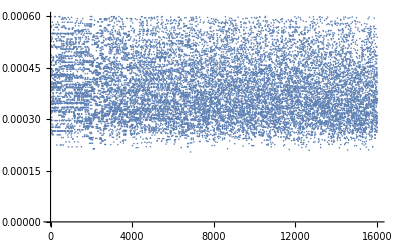

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{}